```mathematica
myPlot[f_,opt:OptionsPattern[]]:=Plot[f@x,{x,0,10},Evaluate[FilterRules[{opt},Options[Plot]]]]
```



```mathematica
myPlot[Sin,ImageSize->Tiny]
```

```mathematica
fs[opts:OptionsPattern[]]:=myPlot[Sin,{PlotLabel->"asa",opts}]
```

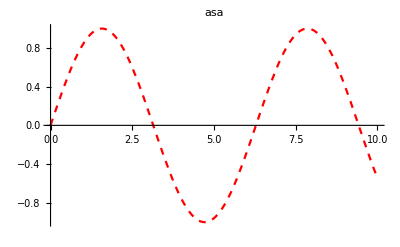

```mathematica
fs[PlotStyle->{Dashed,Red}]
```